## Model setup

```mathematica
f=(η-n^3+0.5n);
source=(p-n);
```

```mathematica
params={eps->10^(-1),Dv->10,p->0,Du->1};
```

## Calcs

```mathematica
jacMC={{0,-Dv*q^2},{Du*q^2-D[f,n]/.{n->0,η->0},-(Du+Dv)*q^2-D[f,η]/.{n->0,η->0}}};
```

```mathematica
evalsMC=Eigenvalues[jacMC];
```

```mathematica
jacLS={{-eps,-Dv*q^2},{Du*q^2-(D[f,n]/.{n->0,η->0})-eps ,-(Du+Dv)*q^2-D[f,η]/.{n->0,η->0}}};
```

```mathematica
evalsLS=Eigenvalues[jacLS];
```

## Plots

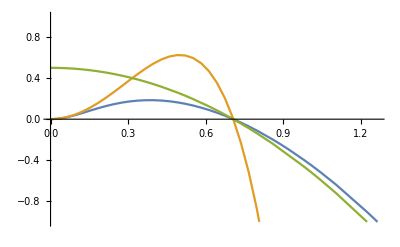

```mathematica
Plot[Evaluate[{evalsMC[[2]],
Dv*q^2*(D[f,n]/D[f,η]/.{n->0,η->0})-Dv*Du*q^2*q^2/D[f,η]/.{n->0,η->0},(D[f,n]/.{n->0,η->0})-Du*q^2}/.params],{q,0,100},
PlotRange->{All,{-1,1}},
AxesStyle->Black,
TicksStyle->Black,
Ticks->{{},{}}]
```

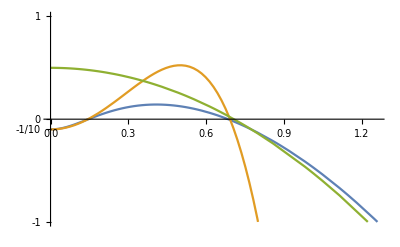

```mathematica
Plot[Evaluate[{evalsLS[[2]],
Dv*q^2*(D[f,n]/D[f,η]/.{n->0,η->0})-Dv*Du*q^2*q^2/(D[f,η]/.{n->0,η->0})-eps,(D[f,n]/.{n->0,η->0})-Du*q^2}/.params],{q,0,50},
PlotRange->{All,{-1,1}},
AxesStyle->Black,
TicksStyle->Black,
Ticks->{{},{-1,-eps/.params,0,1}}]
```